3) Sea el vector posición r⃗que varía con respecto el tiempo de la siguiente forma.

r⃗(t)=( c Cos^3 (t), c Sin^3(t) )

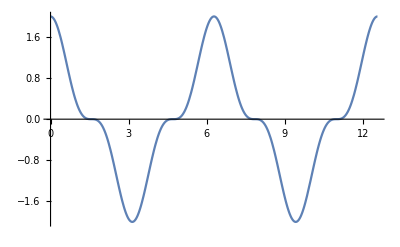

```mathematica
R1x = Plot[c*Cos[t]^3/.c-> 2,{t,0, 4 Pi}]
```

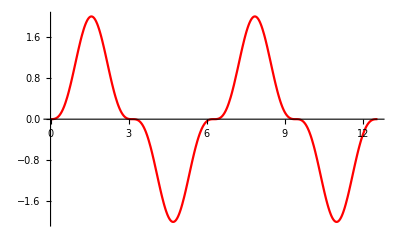

```mathematica
R1y = Plot[c*Sin[t]^3/.c-> 2,{t,0, 4 Pi}, PlotStyle->Red]
```

La velocidad de las componentes de R esta definida como la derivada con respecto al tiempo de sus componentes entonces tenemos lo siguiente.

OverVector[V(t)]= (d OverVector[r(t)])/dt= d/dt(cCos^3(t),cSin^3(t))= ( (d(cCos^3(t)))/dt,(d(c Sin^3(t)))/dt)=(-c 3Sin(t)Cos^2(t) , c 3Cos(t)Sin^2(t))= V⃗(t)

```mathematica
V1x=Plot[-3Sin[t]*Cos[t]^2*c/. c->2, {t,0,4 Pi}];
```

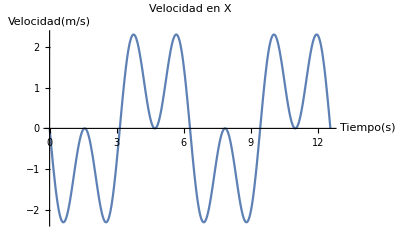

```mathematica
Show[V1x,AxesLabel->{HoldForm[Tiempo[s]],HoldForm[HoldForm[Velocidad[m/s]]]},PlotLabel->"Velocidad en X" ]
```

```mathematica
V1y= Plot[3Cos[t]*Sin[t]^2*c/. c->2, {t,0,4 Pi}, PlotStyle->Red];
```

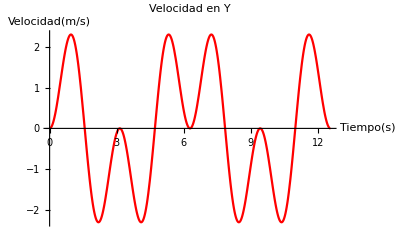

```mathematica
Show[V1y,AxesLabel->{HoldForm[Tiempo[s]],HoldForm[Velocidad[m/s]]},PlotLabel->HoldForm[Velocidad en Y],LabelStyle->{GrayLevel[0]}]
```

Continuamos ahora con la aceleración, tenemos la siguiente formula y desarrollo.

a⃗= (d V⃗)/dt= d/dt(-c 3Sin(t)Cos^2(t) , c 3Cos(t)Sin^2(t))= ( (d(-c 3Sin(t)Cos^2(t)))/dt,(d(c 3Cos(t)Sin^2(t))))/dt)=(c3(2Cos(t)-3 Cos^3(t)) , c3(2Sin(t)-3Sin^3(t)))= a⃗

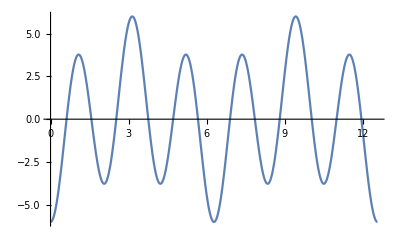

```mathematica
A1x=Plot[3c *(2Cos[t]-3Cos[t]^3)/. c->2, {t,0,4 Pi}]
```

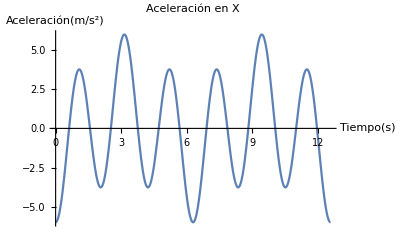

```mathematica
Show[A1x,AxesLabel->{HoldForm[Tiempo[s]],HoldForm[Aceleración[m/s^2]]},PlotLabel->HoldForm[Aceleración en X],LabelStyle->{GrayLevel[0]}]
```

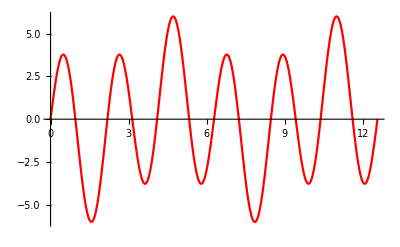

```mathematica
A1y=Plot[3c *(2Sin[t]-3Sin[t]^3)/. c->2, {t,0,4 Pi},PlotStyle->Red]
```

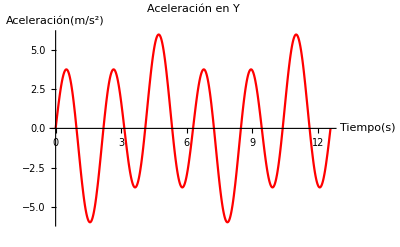

```mathematica
Show[A1y,AxesLabel->{HoldForm[Tiempo[s]],HoldForm[Aceleración[m/s^2]]},PlotLabel->HoldForm[Aceleración en Y],LabelStyle->{GrayLevel[0]}]
```